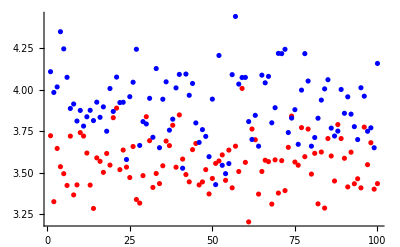

```mathematica
Needs["IGraphM`"]

data26 = BinaryReadList["UU/Scriptie//examples55_26.dat", "Real32"];
data27 = BinaryReadList["UU/Scriptie//examples55_27.dat", "Real32"];
data28 = BinaryReadList["UU/Scriptie//examples55_28.dat", "Real32"];
data29 = BinaryReadList["UU/Scriptie//examples55_29.dat", "Real32"];
data30 = BinaryReadList["UU/Scriptie//examples55_30.dat", "Real32"];
data31 = BinaryReadList["UU/Scriptie//examples55_31.dat", "Real32"];

n=31;
L=100;
gm = ArrayReshape[data31, {L, n, n}];
T = Table[0, L];
L1=T; L2=T;
For[i=1, i<=L, i++,
eigs1 = Sort[N[Eigenvalues[gm[[i]]]]];
L1[[i]]=eigs1[[-3]];
g = AdjacencyGraph[gm[[i]]];
R=IGRewire[g, 1000];
eigs2=Sort[N[Eigenvalues[AdjacencyMatrix[R]]]];
L2[[i]] = eigs2[[-3]];
]
Show[{ListPlot[L1, PlotStyle-> Red], ListPlot[L2, PlotStyle-> Blue]}, PlotRange->All]
```

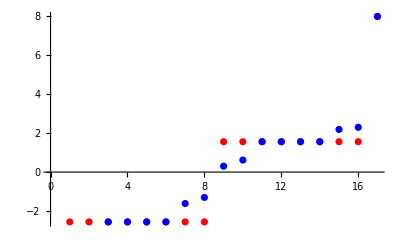

```mathematica
Rgraph = Import["Grafencollectie//r44_17.g6"];
localmin= BinaryReadList["UU/Scriptie//localmin44_17.dat", "Real32"];
localmin = ArrayReshape[localmin, {17,17}];
g = AdjacencyGraph[localmin];
eigsramseygraph = Sort[N[Eigenvalues[AdjacencyMatrix[Rgraph]]]];
eigslocalmin=Sort[N[Eigenvalues[localmin]]];
Show[{ListPlot[eigsramseygraph, PlotStyle->Red], ListPlot[eigslocalmin, PlotStyle->Blue]}]
```

```mathematica
eigslocalmin[[-1]]
eigsramseygraph[[-1]]
```

8.

8.